# Franck Hertz Experiment

# DATA ANALYSIS

Temperature Used : 148 C - 6.5mV for thermoelectric voltage
Bias (voltage applied to accelerating grid 1) - 1.001V

```mathematica
(*TEMPERATURE USED - 148 C *)

data = Import["/Users/gia/Desktop/PHYS2002/Labs/FH/scope_221.csv"];
data=Rest[data];
anodeVoltages=data[[All,2]];
collectorCurrents=data[[All,3]];

anodeVoltages = Drop[anodeVoltages,121]
collectorCurrents = Drop[collectorCurrents,121]

(*found out that last to elements are empty used drop to delete last two elements*)
anodeVoltages=Drop[anodeVoltages,-2]

collectorCurrents=Drop[collectorCurrents,-2]
```

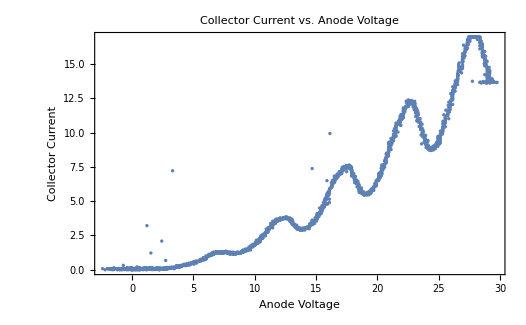

```mathematica
ListPlot[Transpose[{(-1*anodeVoltages),collectorCurrents}],Frame->True,FrameLabel->{"Anode Voltage","Collector Current"},PlotLabel->"Collector Current vs. Anode Voltage"]
```

```mathematica
(*make sure we did not accidentally drop any elements in both lists. *)
```

```mathematica
Length[anodeVoltages]
```

```mathematica
1878
Length[collectorCurrents]
```

1878

```mathematica
1878
```

```mathematica
(*check row  394 to row 484, where voltages are between 6 to 8. *)
anodeVoltages[[394]]
anodeVoltages[[484]]
```

-6.24

-8.049

```mathematica
currentOne = collectorCurrents[[394;;484]]
 voltageOne = anodeVoltages[[394;;484]]

(*use Ordering Function to find the peak where voltages are between 6 to 8*)
Ordering[currentOne,-1]
```

{70}

```mathematica
max1 = voltageOne[[70]]
```

-7.647

```mathematica
(*check from row 584 to 760, where the anodeVoltages are between 10 to 13*)
anodeVoltages[[584]]
anodeVoltages[[760]]
```

-10.059

-13.275

```mathematica
currentTwo = collectorCurrents[[584;;760]]
voltageTwo = anodeVoltages[[584;;760]]
Ordering[currentTwo,-1]
```

{143}

```mathematica
max2 = voltageTwo[[143]]
```

-12.592

```mathematica
(*check from row 915 to 1065, where the anodeVoltages are between 16 to 18*)
anodeVoltages[[915]]
anodeVoltages[[1065]]
```

-16.09

-18.542

```mathematica
currentThree = collectorCurrents[[915;;1065]]
voltageThree = anodeVoltages[[915;;1065]]
Ordering[currentThree,-1]
```

{86}

```mathematica
max3 = voltageThree[[86]]
```

-17.698

```mathematica
(*check from row 1265 to 1389, where the anodeVoltages are between 22 to 24*)
anodeVoltages[[1265]]
anodeVoltages[[1389]]
```

-22.12

-24.13

```mathematica
currentFour = collectorCurrents[[1265;;1389]]
voltageFour = anodeVoltages[[1265;;1389]]
Ordering[currentFour,-1]
```

{40}

```mathematica
max4 = voltageFour[[40]]
```

-22.522

```mathematica
(*check from row 1549 to 1756, where the anodeVoltages are between 26 to 28*)
anodeVoltages[[1549]]
anodeVoltages[[1650]]
```

-26.542

-28.15

```mathematica
currentFive = collectorCurrents[[1549;;1650]]
voltageFive = anodeVoltages[[1549;;1650]]
Ordering[currentFive,-1]
```

{102}

```mathematica
(* maximum current stay at 16.961 for a long time despite the increasing voltage.
we can find the index of the first occurrence of a 16.961 in the list using the Position function. *)
position = FirstPosition[currentFive,16.961]
```

{66}

```mathematica
max5 =voltageFive[[66]]
```

-27.547

```mathematica
(*Determine the excitation energy of the mercury atoms*)

peaks = {-max1,-max2,-max3,-max4,-max5}

energy = {0,0,0,0}

(* find the differences of successive peaks, then put it in the 'energy' list*)

For[i=1,i<5,i++,
energy[[i]] =peaks[[i+1]] - peaks[[i]] 
]
```

{7.647,12.592,17.698,22.522,27.547}

{0,0,0,0}

```mathematica
energy

meanE = Mean[energy]
```

{4.945,5.106,4.824,5.025}

4.975

```mathematica
(*find the associated error*)
StandardDeviation[energy]
```

0.120225

```mathematica
(*Determine Contact Potential Difference = First excitation energy - average excitation energy*)
contactPD = (-max1) - meanE
```

2.672

```mathematica
discharge Electric gases in
```

# VARIATION OF OVEN TEMPERATURE

Temperature Used : 156 C - 7.0mV for thermoelectric voltage
Bias (voltage applied to accelerating grid 1) - 1.003V

```mathematica
data2 = Import["/Users/gia/Desktop/PHYS2002/Labs/FH/scope_25.csv"];
data2=Rest[data2];
anodeVoltages2=data2[[All,2]];
collectorCurrents2=data2[[All,3]];

anodeVoltages2 = Drop[anodeVoltages2,451]
collectorCurrents2 = Drop[collectorCurrents2,451]
```

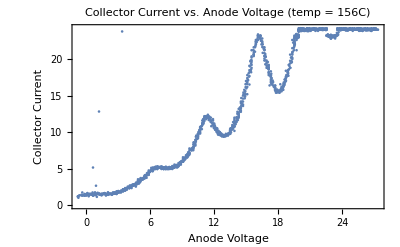

```mathematica
ListPlot[Transpose[{anodeVoltages2,collectorCurrents2}],Frame->True,FrameLabel->{"Anode Voltage","Collector Current"},PlotLabel->"Collector Current vs. Anode Voltage (temp = 156C)"]
```

```mathematica
(*check row  352 to row 392, where voltages are between 6 to 7. *)
anodeVoltages2[[352]]
anodeVoltages2[[392]]
```

6.051

6.855

```mathematica
currentA = collectorCurrents2[[352;;392]]
 voltageA = anodeVoltages2[[352;;392]]

(*use Ordering Function to find the peak where voltages are between 6 to 7*)
Ordering[currentA,-1]
```

{36}

```mathematica
p1 = voltageA[[36]]
```

6.694

```mathematica
(*check row  601 to row 665, where voltages are between 11 to 12. *)
```

```mathematica
anodeVoltages2[[601]]
anodeVoltages2[[665]]
```

10.875

12.242

```mathematica
currentB = collectorCurrents2[[601;;665]]
 voltageB = anodeVoltages2[[601;;665]]
Ordering[currentB,-1]
```

```mathematica
{19}
```

{19}

```mathematica
p2 = voltageB[[19]]
```

11.398

```mathematica
(*check row  601 to row 665, where voltages are between 15 to 17. *)
```

```mathematica
anodeVoltages2[[820]]
anodeVoltages2[[922]]
```

15.136

17.106

```mathematica
currentC = collectorCurrents2[[820;;922]]
 voltageC = anodeVoltages2[[820;;922]]
Ordering[currentC,-1]
```

{58}

```mathematica
p3 = voltageC[[58]]
```

16.101

```mathematica
peaksTemp = {p1,p2,p3}

energyTemp = {0,0}

(* find the differences of successive peaks, then put it in the 'energyTemp' list*)
For[i=1,i<3,i++,
energyTemp[[i]] =peaksTemp[[i+1]] - peaksTemp[[i]] 
] 

(*find mean excitation *)
meanETemp = Mean[energyTemp]
```

{6.694,11.398,16.101}

{0,0}

4.7035

```mathematica
(*associated error*)
StandardDeviation[energyTemp]
```

0.000707107

# VARIATION OF ACCELERATING GRID 1 VOLTAGE

Temperature  - 156C
Acc grid 1 voltage - 2.0V

```mathematica
(*TEMPERATURE USED - 156C*)
(*Acc grid 1 voltage - 2.0V*)
```

```mathematica
data3 = Import["/Users/gia/Desktop/PHYS2002/Labs/FH/scope_28.csv"];
data3=Rest[data3];
anodeVoltages3=data3[[All,2]];
collectorCurrents3=data3[[All,3]];
anodeVoltages3 = Drop[anodeVoltages3,1]
collectorCurrents3 = Drop[collectorCurrents3,1]
```

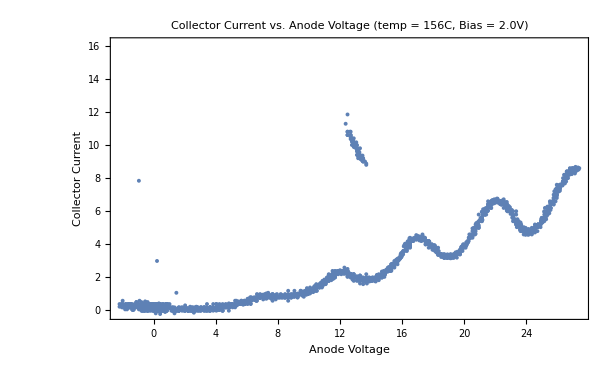

```mathematica
ListPlot[Transpose[{anodeVoltages3,collectorCurrents3}],Frame->True,FrameLabel->{"Anode Voltage","Collector Current"},PlotLabel->"Collector Current vs. Anode Voltage (temp = 156C, Bias = 2.0V)"]
```